# On-chip MBQC machines of NV-center

## VQD setup

Set the main directory as the current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink package
One may also use the off-line questlink.m file, change it to the location of the local file

```mathematica
Quiet@Import["https://qtechtheory.org/questlink.m"]
```

This will download a binary file  quest_link from the repo; some error will show if the system tries to override the file
Use CreateLocalQuESTEnv[quest_link_file] if the binary has already exists

```mathematica
(*CreateDownloadedQuESTEnv[];*)
CreateLocalQuESTEnv["quest_link"];
```

Load the VQD package; must be loaded after QuESTlink is loaded

```mathematica
Import["https://raw.githubusercontent.com/QTechTheory/VQD/refs/heads/master/vqd.wl"]
```

## Native gates

Direct iIitialisation and measurement are on the NV electron spin only
Init_0, M_0
Single-qubit gates
Rx_q[θ], Ry_q[θ], Rz_q[θ] 
Two-qubit gates are conditional rotation, where  CRσ[θ]:=|0X0|⊗ Rσ[θ]+|1X1|⊗ Rσ[-θ]
CRx_(0,q)[θ], CRy_(0,q)[θ]
others: doing nothing
Wait_q[duration]

## User device configuration

Qubit 0 indicates electron spin,and the rest are nuclear spins  C^13 and N^14 - if applicable
Time unit is second (s)
Frequency unit is  Hertz (Hz)

In the following example, we have a 4-qubit system. Q0 -> Electronic spin qubit and the rest are Nuclear spin qubits

```mathematica
Options[NVCenterDelft]={
QubitNum->4,
(* T1 of each qubit *)
T1-> <|0-> 3600,1->60,2->60,3->60 |>,
(* T2 of each qubit; we assume dynamical decoupling is actively applied *)
T2-> <|0-> 1.5,1->10,2->10,3->10|>,
(* dipolar interaction among nuclear spins: cross-talk ZZ-coupling in order of a few Hz on passive noise *)
FreqWeakZZ->5,
(* direct single rotation on Nuclear spin is done via RF, put electron in state -1 leave out the Rx Ry on nuclear spins ideally. *)
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500|>,
(* usually done virtually *)
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3|>,
(* Frequency of CRot gate, conditional rotation done via dynamical decoupling or dd+RF. The gate is conditioned on electron spin state *)
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3|>,
(* Fidelity of CRot gate  *)
FidCRot-><|1-> 0.98,2->0.98, 3->0.98|>,
(* fidelity of x- and y- rotations on each qubit *)
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99|>,
(* fidelity of z- rotations on each qubit *)
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999 |>,
(* Error ratio of 1-qubit depolarising:dephasing of x- and y- rotations  *)
EFSingleXY->{0.75,0.25},
(* Error ratio of 2-qubit depolarising:dephasing of CRot gate *)
EFCRot->{0.9,0.1},
(* initialization fidelity on the electron spin *)
FidInit-> 0.999,
(* initialization duration on the electron spin *)
DurInit->2*10^-3,
(* measurement fidelity on the electron spin *)
FidMeas->0.946,
(* measurement duration on the electron spin *)
DurMeas->2*10^-5,
(* Switch to standard passive noise *)
StdPassiveNoise -> True
};
```

-Graphics-

```mathematica
NVDevice=NVCenterDelft[];
```

```mathematica
NVNoise=<|"description"->"On Chip NVCenter with explicit electronic spin"|>;
```

## QuESTlink and convention

QuEST uses Least Significant Bit
QuEST uses Superopeator to store and perform operation on density matrices

By LSB, therefore:
Column-stacking:  A_(i,j)|i X j| :> A_(i,j)j i : { 00, 10, 01, (11})_(q0, q1),  in QuEST: {00,01,10,11}_(q1,q0)
Row-stacking: A_(i,j)|i X j| :> A_(i,j)i j: {00, 01, 10, (11})_(q0,q1), in QuEST: {00,10,01,11}_(q1,q0)

## Noise channel optimisation

```mathematica
ClearAll[hermitianTemplate]
hermitianTemplate::usage="hermitianTemplate[dim, variable(or {diag, real, imag}), [init_matrix]]. 
Create template for hermitian matrix. Returns {hermitian template, elements, elements_constraints, initial values} with initial value as unnormalized bell state |00>+|11>. Note that the resulting hermitian operator is in choi form.";
hermitianTemplate[n_, var_List] := Module[{d, a, z, superop, elemconst, initval, elems},
	{d, a, z} = var;
	(* symbolic superoperator *)
	superop = DiagonalMatrix[Array[Subscript[d, #,#]&, {n}]];
	Table[
		superop[[r, c]] = Subscript[a, r,c] + ⅈ Subscript[z, r,c];
		superop[[c, r]] = Subscript[a, r,c] - ⅈ Subscript[z, r,c]
		,{r, n}, {c, r+1, n}];
		
	(* elements *)
	elems = Flatten @ {Table[Subscript[d, i,i] ∈ Reals, {i, n}],
				Table[{Subscript[a, r,c] ∈ Reals, Subscript[z, r,c]  ∈ Reals}, {r, n}, {c, r + 1, n}]};
	
	(* constraint on each element *)
	elemconst = Flatten[
		{ 
		(* diagonal constraint is probability value *)
		(0 <= Subscript[d, #,#] <= 1)& /@ Range[n], 
		(* off-diagonal constraint is complex disk with radius 1 *)
		Table[Table[
			Sqrt[Subscript[a, row, col]^2 + Subscript[z, row, col]^2] <= 1
			, {col, row + 1, n}], {row, n}]
		}
		];
	(* initial value as an identity matrix *)
	initval = Association @ Flatten[
		{ 
		Subscript[d, #, #] -> 0 &  /@ Range[n], 
		Table[Table[Subscript[a, row, col] -> 0, {col, row + 1, n}], {row, n}],
		Table[Table[Subscript[z, row, col] -> 0, {col, row + 1, n}], {row, n}]
		}
		];
	initval[Subscript[d, 1,1]]=1;
	initval[Subscript[d, 4,4]]=1;
	initval[Subscript[a, 1,4]]=1;
	{superop, elems, elemconst, Normal @ initval}		
]
```

## Preparation operation

XY-plane basis: +_θ= {1/(√2),ⅇ^(ⅈ θ)/(√2)} and -_θ={1/(√2),-ⅇ^(ⅈ θ)/(√2)}
 Note that, NV center has star connectivity . Initialisation of the qubit happens on the center qubit (electron spin qubit) . See “Native Gates” section
 My strategy here is prepare the state in the center, then perform partial SWAP to the edge qubits (Nuclear spin qubits).
 Here we do not need the full swap because the states are rebits (Real qubits)

```mathematica
xyDensityMatrix::usage="xyDensityMatrix[θ]. Create rebit in XY plane with parameter θ";
xyDensityMatrix[θ_]:=KroneckerProduct[{1/(√2),ⅇ^(ⅈ θ)/(√2)},{1/(√2),ⅇ^(-ⅈ θ)/(√2)}]
```

In vector simulation, the state can be obtained by two single rotations. The following operations show the ideal case should be able to prepare any XY-state
This direct operation can be done on the electronic spin

```mathematica
mat = CalcCircuitMatrix[{Subscript[Ry, 0][π/2],Subscript[Rz, 0][θ]}]
```

{{ⅇ^(-(ⅈ θ)/2)/(√2),-ⅇ^(-(ⅈ θ)/2)/(√2)},{ⅇ^((ⅈ θ)/2)/(√2),ⅇ^((ⅈ θ)/2)/(√2)}}

```mathematica
(* State +θ*)
ⅇ^(ⅈ θ/2)*mat.{1,0}
```

{1/(√2),ⅇ^(ⅈ θ)/(√2)}

```mathematica
(* State -θ*)
-ⅇ^(ⅈ θ/2)*mat.{0,1}
```

{1/(√2),-ⅇ^(ⅈ θ)/(√2)}

### Prepare XY - state on the electron spin

```mathematica
xyElectron[θ_]:=Sequence@@{Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[Rz, 0][θ]}
```

```mathematica
Flatten[{xyElectron[θ]}/.NVDevice[Aliases]]
supop1=CalcCircuitMatrix@%
```

{Damp_0[1.],Ry_0[π/2],Rz_0[θ]}

{{0.5,0.,0.,0.5},{0.+0.5 ⅇ^(ⅈ θ),0.,0.,0.+0.5 ⅇ^(ⅈ θ)},{0.+0.5 ⅇ^(-ⅈ θ),0.,0.,0.+0.5 ⅇ^(-ⅈ θ)},{0.5,0.,0.,0.5}}

Density matrix test: Start with an arbirary random mix density matrix  and see if the electron spin is initialised to the XY-plane states

```mathematica
ρmat1=RandomMixState@1
```

{{0.246115,0.255874-0.346105 ⅈ},{0.255874+0.346105 ⅈ,0.753885}}

```mathematica
(* Superoperate *)
Chop@SuperOperate[ρmat1, supop1]
(* compare to the GOAL*)
Chop@N@xyDensityMatrix@θ
```

{{0.5,0.5 ⅇ^(-ⅈ θ)},{0.5 ⅇ^(ⅈ θ),0.5}}

{{0.5,0.5 2.71828^((0.-1. ⅈ) θ)},{0.5 2.71828^((0.+1. ⅈ) θ),0.5}}

### Prepare XY - state on the nuclear spin

```mathematica
Subscript[xyNuclear, q_/;q>0][θ_]:=Sequence@@{Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[CRx, 0,q][π/2],Subscript[Rx, 0][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Ry, q][π/2],Subscript[Rz, q][θ]}
```

```mathematica
Flatten[{Subscript[xyNuclear, 1][θ]}/.NVDevice[Aliases]]
supop2=CalcCircuitMatrix@%;
```

{Damp_0[1.],Ry_0[π/2],U_(0,1)[{{1/(√2),0,-ⅈ/(√2),0},{0,1/(√2),0,ⅈ/(√2)},{-ⅈ/(√2),0,1/(√2),0},{0,ⅈ/(√2),0,1/(√2)}}],Rx_0[π/2],U_(0,1)[{{1/(√2),0,1/(√2),0},{0,1/(√2),0,-1/(√2)},{-1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)}}],Ry_1[π/2],Rz_1[θ]}

Density matrix test: Start with an arbirary random mix density matrix  and see if the nuclear spin is initialised to the XY-plane states

```mathematica
ρmat2=RandomMixState@2
```

{{0.130573,-0.0320415-0.152548 ⅈ,0.0473175+0.0529285 ⅈ,0.115754-0.0615628 ⅈ},{-0.0320415+0.152548 ⅈ,0.297148,-0.0713879+0.124337 ⅈ,-0.00876279+0.240503 ⅈ},{0.0473175-0.0529285 ⅈ,-0.0713879-0.124337 ⅈ,0.306115,0.0258955-0.0466347 ⅈ},{0.115754+0.0615628 ⅈ,-0.00876279-0.240503 ⅈ,0.0258955+0.0466347 ⅈ,0.266164}}

```mathematica
(* Superoperate, then trace the electron spin *)
PartialTrace[Chop@SuperOperate[ρmat2, supop2],0]
(* compare to the GOAL*)
xyDensityMatrix@θ
```

{{0.5,0.5 ⅇ^(-ⅈ θ)},{0.5 ⅇ^(ⅈ θ),0.5}}

{{1/2,ⅇ^(-ⅈ θ)/2},{ⅇ^(ⅈ θ)/2,1/2}}

## FULL NOISE: preparation

### Noisy preparation of the electron spin to state +θ

```mathematica
elprep={xyElectron[θ]}
```

{Init_0,Ry_0[π/2],Rz_0[θ]}

Note that here is only preparing the electronic spin state to XY plane. Notice the presence of Cross-talk are forming all-to-all connectivity

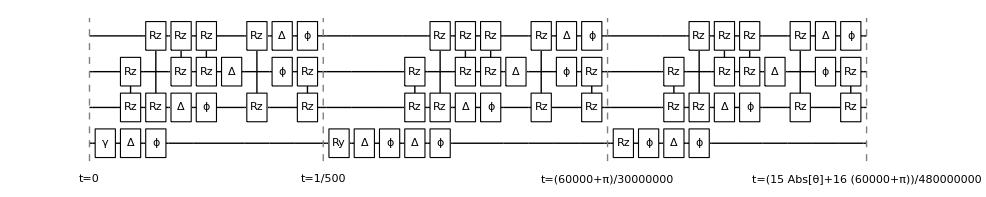

```mathematica
elprepNoisy=Assuming[Element[θ,Reals],Simplify@InsertCircuitNoise[elprep,NVDevice,ReplaceAliases->True]];
DrawCircuit@%
```

Try all states from the same random density matrix

```mathematica
DestroyAllQuregs[]
```

```mathematica
ρ4=CreateDensityQureg[4]
```

0

```mathematica
ρinit=RandomMixState@4;
Grid@Table[
param=j π/4;
noisycirc=ExtractCircuit[ elprepNoisy/.θ->param];
(* cross check, if superoperate operates the same way as QuEST*)
SetQuregMatrix[ρ4,ρinit];
ApplyCircuit[ρ4,noisycirc];
ρetom=PartialTrace[GetQuregState@ρ4,1,2,3];
ρeid=xyDensityMatrix[param];
{param, CalcFidelityDensityMatrices[ρetom,ρeid],MatrixForm@Chop@ρetom, MatrixForm@Chop@N@ρeid}
,{j,0,7}]
```

0 | 0.999194 | (0.498942 | 0.499194-0.000328665 ⅈ
0.499194+0.000328665 ⅈ | 0.501058) | (0.5 | 0.5
0.5 | 0.5)
π/4 | 0.999156 | (0.498942 | 0.352725-0.353189 ⅈ
0.352725+0.353189 ⅈ | 0.501058) | (0.5 | 0.353553-0.353553 ⅈ
0.353553+0.353553 ⅈ | 0.5)
π/2 | 0.999119 | (0.498942 | -0.000328616-0.499119 ⅈ
-0.000328616+0.499119 ⅈ | 0.501058) | (0.5 | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5)
(3 π)/4 | 0.999082 | (0.498942 | -0.353136-0.352672 ⅈ
-0.353136+0.352672 ⅈ | 0.501058) | (0.5 | -0.353553-0.353553 ⅈ
-0.353553+0.353553 ⅈ | 0.5)
π | 0.999044 | (0.498942 | -0.499044+0.000328567 ⅈ
-0.499044-0.000328567 ⅈ | 0.501058) | (0.5 | -0.5
-0.5 | 0.5)
(5 π)/4 | 0.999007 | (0.498942 | -0.352619+0.353083 ⅈ
-0.352619-0.353083 ⅈ | 0.501058) | (0.5 | -0.353553+0.353553 ⅈ
-0.353553-0.353553 ⅈ | 0.5)
(3 π)/2 | 0.998969 | (0.498942 | 0.000328517+0.498969 ⅈ
0.000328517-0.498969 ⅈ | 0.501058) | (0.5 | 0.+0.5 ⅈ
0.-0.5 ⅈ | 0.5)
(7 π)/4 | 0.998932 | (0.498942 | 0.35303+0.352566 ⅈ
0.35303-0.352566 ⅈ | 0.501058) | (0.5 | 0.353553+0.353553 ⅈ
0.353553-0.353553 ⅈ | 0.5)

### Noisy preparation of the nuclear spin to state +θ

```mathematica
nuprep={Subscript[xyNuclear, 1][θ]}
```

{Init_0,Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2],Ry_1[π/2],Rz_1[θ]}

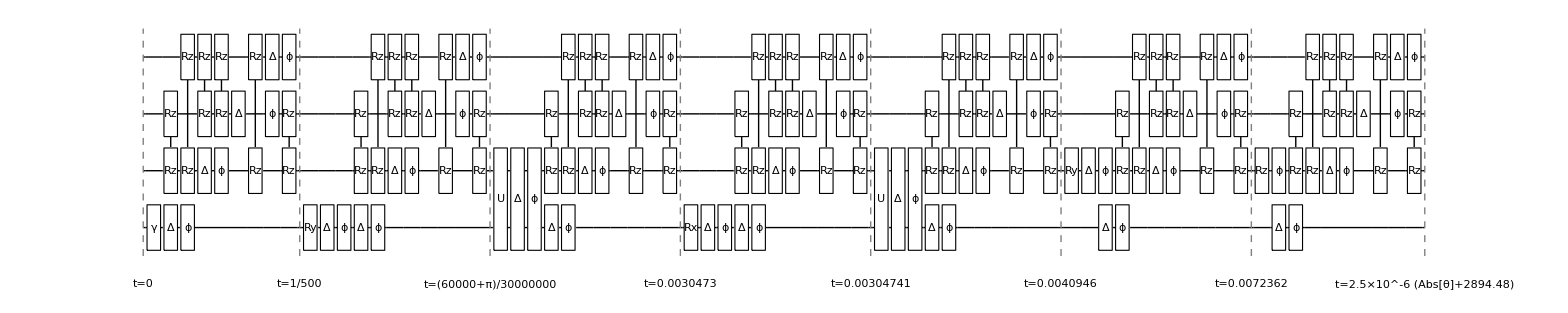

```mathematica
nuprepNoisy=Assuming[Element[θ,Reals],Simplify@InsertCircuitNoise[nuprep,NVDevice,ReplaceAliases->True]];
DrawCircuit@%
```

```mathematica
durprep=First@Last@nuprepNoisy
```

2.5×10^-6 (2894.48+Abs[θ])

```mathematica
(* Start with a complete mixed state for consistent result *)
ρinit=IdentityMatrix[2^4]/2^4;
resPrepNuclear=Table[
param=j π/4;
noisycirc=ExtractCircuit[ nuprepNoisy/.θ->param];
(* Cross check, if superoperate operates the same way as QuEST *)
SetQuregMatrix[ρ4,ρinit];
ApplyCircuit[ρ4,noisycirc];
ρetom=PartialTrace[GetQuregState@ρ4,0,2,3];
ρeid=xyDensityMatrix[param];
{param, CalcFidelityDensityMatrices[ρetom,ρeid],ρetom,ρeid}
,{j,0,7}];
```

```mathematica
Grid[{#[[1]],#[[2]],TraditionalForm@Chop@#[[3]],TraditionalForm@Chop@N@#[[4]]}&/@resPrepNuclear]
```

0 | 0.983547 | (0.5 | 0.483547
0.483547 | 0.5) | (0.5 | 0.5
0.5 | 0.5)
π/4 | 0.98351 | (0.5 | 0.341893-0.341893 ⅈ
0.341893+0.341893 ⅈ | 0.5) | (0.5 | 0.353553-0.353553 ⅈ
0.353553+0.353553 ⅈ | 0.5)
π/2 | 0.983474 | (0.5 | 0.-0.483474 ⅈ
0.+0.483474 ⅈ | 0.5) | (0.5 | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5)
(3 π)/4 | 0.983438 | (0.5 | -0.341842-0.341842 ⅈ
-0.341842+0.341842 ⅈ | 0.5) | (0.5 | -0.353553-0.353553 ⅈ
-0.353553+0.353553 ⅈ | 0.5)
π | 0.983402 | (0.5 | -0.483402
-0.483402 | 0.5) | (0.5 | -0.5
-0.5 | 0.5)
(5 π)/4 | 0.983365 | (0.5 | -0.341791+0.341791 ⅈ
-0.341791-0.341791 ⅈ | 0.5) | (0.5 | -0.353553+0.353553 ⅈ
-0.353553-0.353553 ⅈ | 0.5)
(3 π)/2 | 0.983329 | (0.5 | 0.+0.483329 ⅈ
0.-0.483329 ⅈ | 0.5) | (0.5 | 0.+0.5 ⅈ
0.-0.5 ⅈ | 0.5)
(7 π)/4 | 0.983293 | (0.5 | 0.34174+0.34174 ⅈ
0.34174-0.34174 ⅈ | 0.5) | (0.5 | 0.353553+0.353553 ⅈ
0.353553-0.353553 ⅈ | 0.5)

## GRAPHIX noise extraction: nuclear spin preparation

```mathematica
ClearAll[ChoiToKraus]
ChoiToKraus::usage="Transform Choi matrix to Kraus map form.";
ChoiToKraus[choi_]:=With[{kraus = Sqrt[#[[1]]]*Tensorize[#[[2]], Stacking->"column"]& /@ (Transpose @ Eigensystem[choi])},
	Assert[Chop@Total[#.ConjugateTranspose[#]& /@ kraus] === IdentityMatrix[Length@kraus[[1]]], "Kraus decomposition failed to be complete."];
	kraus
]
```

{Init_0,Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2],Ry_1[π/2],Rz_1[θ]}

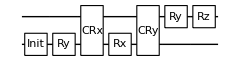

```mathematica
nuprep={Subscript[xyNuclear, 1][θ]}
DrawCircuit@%
```

1) Remove passive noise: cross-talk and exponential decay will disappear

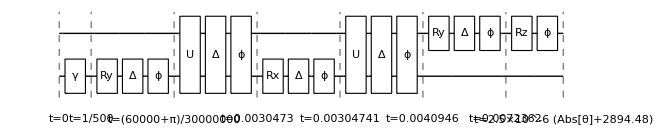

```mathematica
nuprepNoisy=Assuming[Element[θ,Reals],Simplify@InsertCircuitNoise[nuprep,NVCenterDelft[FreqWeakZZ->False,StdPassiveNoise->False],ReplaceAliases->True]];
DrawCircuit@%
```

```mathematica
ρ2=CreateDensityQureg[2]
```

1

### 1) Final gate noise, approximation of Ε(+θ)

```mathematica
ngPrep = Table[
	param = j π/4;
	noisycirc=ExtractCircuit[nuprepNoisy/.θ->param];
	SetQuregMatrix[ρ2, IdentityMatrix[2^2]/2^2]; (* maximally mixed state *)
	ApplyCircuit[ρ2, noisycirc];
	ρtomo=Chop@PartialTrace[GetQuregState@ρ2, 0];
	ρideal=N@xyDensityMatrix[param];
	{choiop, elems,constrains,init} = hermitianTemplate[4, {d,a,b}];
	xrpt2 =(TensorContract[ArrayReshape[choiop, {2, 2, 2, 2}], {2, 4}] == IdentityMatrix[2]);
	cost = Simplify[ExpandAll@Norm[ChoiApply[ρideal, choiop]-ρtomo,"Frobenius"], elems];
	sol = ConvexOptimization[cost, {VectorGreaterEqual[{choiop, 0}, {"SemidefiniteCone", 4}],xrpt2}, elems, PerformanceGoal-> "Quality"];
	kraus = ChoiToKraus[choiop/.sol];
	(* test*)
	Print@{param, Norm[Total[#.ρideal.ConjugateTranspose[#]&/@kraus]-ρtomo,1], CalcFidelityDensityMatrices[ρtomo, ρideal]};
	ToString[j] -> {Chop @ Re @ kraus, Chop @ Im @ kraus}
,{j,0,7}];
```

{0,1.91374×10^-11,0.983547}

{π/4,0.483511,0.983511}

{π/2,4.49429×10^-11,0.983475}

{(3 π)/4,0.483439,0.983439}

{π,1.28669×10^-11,0.983402}

{(5 π)/4,0.483366,0.983366}

{(3 π)/2,4.39655×10^-11,0.98333}

{(7 π)/4,0.483294,0.983294}

```mathematica
(* Check fidelity using the kraus map *)
Table[
ρideal=N@xyDensityMatrix[j π/4];
kraus=ngPrep[[j+1]][[2]];
kmap=kraus[[1]]+ⅈ kraus[[2]];
ρtomo=Total[#.ρideal.ConjugateTranspose[#]&/@ kmap];
CalcFidelityDensityMatrices[ρideal,ρtomo]
,{j, 0,7}]
```

{0.983547,0.5,0.983475,0.5,0.983402,0.5,0.98333,0.5}

```mathematica
(*NVNoise["ngPrep"]=ngPrep;*)
```

```mathematica
(*NVNoise["durPrep"]=Table[ToString[j] -> First@Last@nuprepNoisy/.θ->j π/4 , {j, 0, 7}]*)
```

### 2) Directly using noisy gate Λ_θ

```mathematica
Table[
param=j π/4;
SetQuregMatrix[ρ2,IdentityMatrix[4]/4];
ApplyCircuit[ρ2,ExtractCircuit[nuprepNoisy/.θ->param]];
ρtomo=Chop@PartialTrace[GetQuregState[ρ2],0];
CalcFidelityDensityMatrices[ρtomo,xyDensityMatrix[param]]
,{j,0,7}]
```

{0.983547,0.983511,0.983475,0.983439,0.983402,0.983366,0.98333,0.983294}

```mathematica
op=CalcCircuitMatrix[Subscript[Rz, 0][θ],AsSuperoperator->True]
```

{{1,0,0,0},{0,ⅇ^(ⅈ θ),0,0},{0,0,ⅇ^(-ⅈ θ),0},{0,0,0,1}}

```mathematica
ρ=CreateDensityQureg@1;
plus=GetQuregState@InitPlusState@ρ
```

{{0.5+0. ⅈ,0.5+0. ⅈ},{0.5+0. ⅈ,0.5+0. ⅈ}}

```mathematica
ngPrep=Table[
param =j π/4;
superopprep=CalcCircuitMatrix[ExtractCircuit[nuprepNoisy]/.θ->param];
kraus=Chop@ChoiToKraus@ColumnShuffle@superopprep; 
(* test to prepare state from random mixed state, and check fidelity *)
ρinit=IdentityMatrix[4]/4;
(*ρtomo=SuperOperate[ρinit,superopprep, Stacking->"column"]; *)
ρtomo=Total[#.ρinit.ConjugateTranspose[#]& /@ kraus];
Print@CalcFidelityDensityMatrices[PartialTrace[ρtomo,0],xyDensityMatrix[param]];
ToString[j] -> {Chop @ Re @ kraus, Chop @ Im @ kraus}
,{j,0,7}];
```

0.983547

0.983511

0.983475

0.983439

0.983402

0.983366

0.98333

0.983294

```mathematica
NVNoise["ngPrep"]=ngPrep;
NVNoise["durPrep"]=Table[ToString[j] -> First@Last@nuprepNoisy/.θ->j π/4 , {j, 0, 7}]
```

{0→0.0072362,1→0.00723816,2→0.00724012,3→0.00724209,4→0.00724405,5→0.00724601,6→0.00724798,7→0.00724994}

## CZ operations

## CZ operation between electron-nuclear spin

```mathematica
Subscript[CZen, q_/;q>0] := Sequence @@ {Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2], Subscript[Rz, 0][-π/2], Subscript[Ry, q][π/2], Subscript[Rx, q][-π/2]}
```

```mathematica
MatrixForm[ Chop[ⅇ^(-ⅈ  π/4)CalcCircuitMatrix@Flatten[{Subscript[CZen, 1]}/.NVDevice[Aliases]]]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

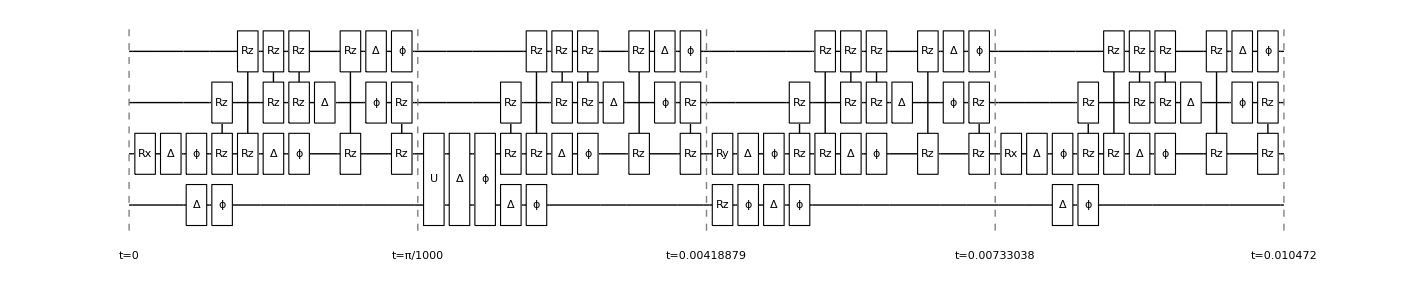

```mathematica
noisycze=InsertCircuitNoise[{Subscript[CZen, 1]}, NVDevice,ReplaceAliases->True];
DrawCircuit@%
```

## CZ operation between nuclear - nuclear spin

CZ operation between nuclear-nuclear spins uses the following tricks:
SWAP the state of nuclear spin to the electron spin , CZe, SWAP again

```mathematica
Subscript[CXen, q_/;q>0]:=Sequence @@ {Subscript[CRx, 0,q][π/2],Subscript[Rz, 0][-π/2],Subscript[Rx, q][-π/2]};
Subscript[SWAPen, q_/;q>0]:=Sequence@@{Subscript[CXen, q],Subscript[Ry, 0][-π/2],Subscript[Rz, 0][π],Subscript[Ry, q][-π/2],Subscript[Rz, q][π],Subscript[CXen, q],Subscript[Ry, 0][-π/2],Subscript[Rz, 0][π],Subscript[Ry, q][-π/2],Subscript[Rz, q][π],Subscript[CXen, q]};
Subscript[CZnn, q1_/;q1>0,q2_/;q2>0]:=Sequence@@{Subscript[SWAPen, q1],Subscript[CZen, q2],Subscript[SWAPen, q1]}
```

```mathematica
(* Check if the SWAP works *)
MatrixForm[ⅇ^(-ⅈ 3π/4)CalcCircuitMatrix@Flatten[{Subscript[SWAPen, 1]}/.NVDevice[Aliases]]]
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
(* Check if CZ between two-nuclear spins works *)
ExpandAll[(ⅇ^((ⅈ π)/4)/4+ⅈ ⅇ^((-ⅈ π)/4)/4)*PartialTrace[CalcCircuitMatrix@Flatten[{Subscript[CZnn, 1,2]}/.NVDevice[Aliases]],0]]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}

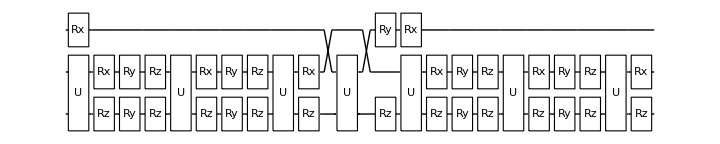

```mathematica
(* This looks overkill!!! :( *)
DrawCircuit@Flatten[{Subscript[CZnn, 1,2]}/.NVDevice[Aliases]]
```

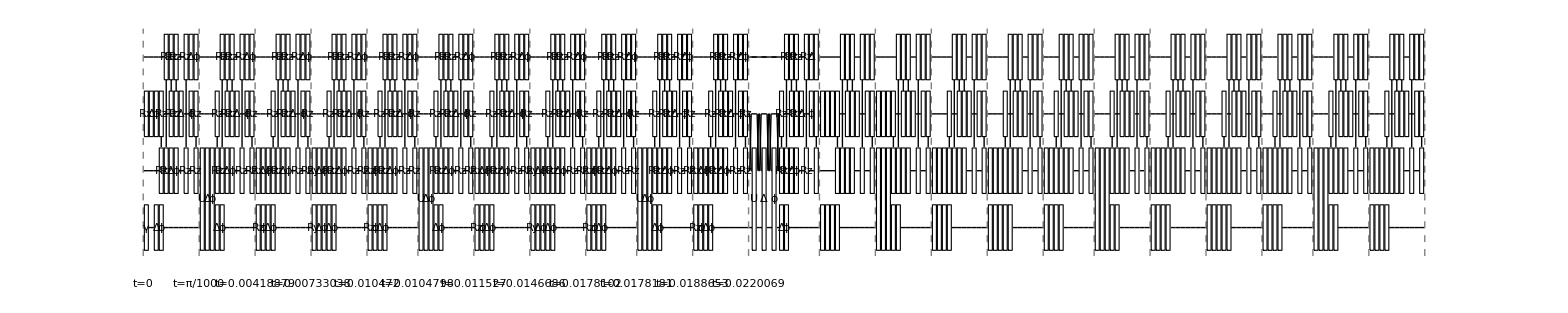

```mathematica
noisycznn=InsertCircuitNoise[{Subscript[Init, 0],Subscript[CZnn, 1,2]}, NVDevice,ReplaceAliases->True];
DrawCircuit@%
```

```mathematica
Length@{Subscript[CZnn, 1,2]}
```

39

## GRAPHIX noise extraction:noisy CZ-operation

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, plotglobalphase:False]. Calculate distance of 2 matrices by max_λ |(U-V)|, 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,plotglobalphase_:False]:=Module[{globalphase,mindist,F,ϕ},
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"}]];
{mindist,ϕ/.globalphase}
]

ChoiDist[C1_, C2_] := Re[Tr[C1.C2]/Sqrt[Tr[C1.C1]*Tr[C2.C2]]]
```

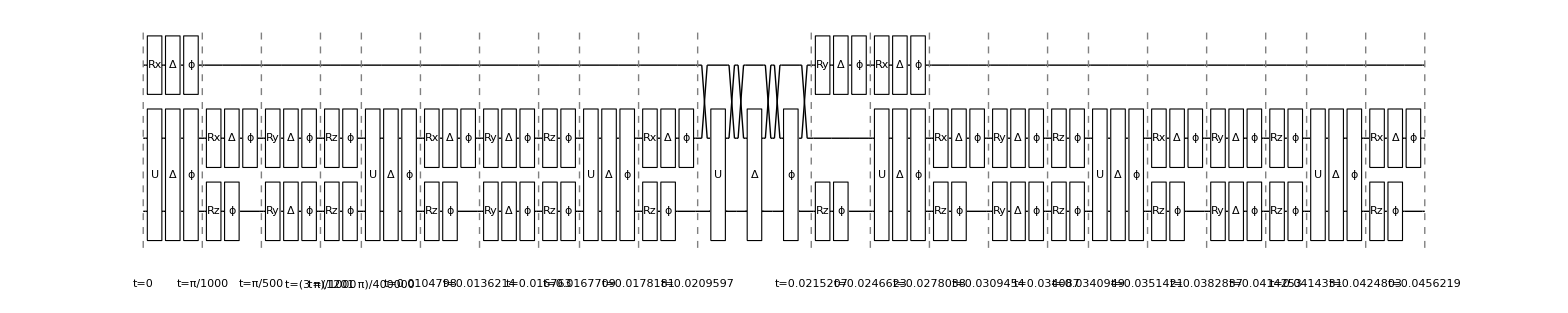

```mathematica
noisycznn=InsertCircuitNoise[{Subscript[CZnn, 1,2]}, NVCenterDelft[StdPassiveNoise->False, FreqWeakZZ->False],ReplaceAliases->True];
DrawCircuit@%
```

```mathematica
supopnoisycz=CalcCircuitMatrix@ExtractCircuit@noisycznn;
krausnoisycz=Chop@ChoiToKraus@ColumnShuffle@supopnoisycz;
```

```mathematica
NVNoise["ngCZ"]={Re@krausnoisycz,Im@krausnoisycz};
NVNoise["durCZ"]=First@Last@noisycznn;
```

```mathematica
(* Check the operator distances and fidelity *)
cznn12=CalcCircuitMatrix[Flatten[{Subscript[CZnn, 1,2]}/.NVDevice[Aliases]],AsSuperoperator->True];
cz12=CalcCircuitMatrix[Subscript[C, 1][Subscript[Z, 2]],AsSuperoperator->True];
```

```mathematica
(* Check fidelity on the clean gate*)
ChoiDist[ColumnShuffle@cznn12,ColumnShuffle@cz12]
```

1

```mathematica
ChoiDist[ColumnShuffle@supopnoisycz,ColumnShuffle@cz12]
```

0.999473

### Directly use the noisy gate

## Measurement

```mathematica
(*measurement sequences on nuclear spins the computational basis *)
Subscript[measZ, q_ /; q>0] := Sequence[Subscript[Ry, 0][π/2],Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Rx, 0][π/2],Subscript[M, 0]]
(*measurement sequences on nuclear spins the XY basis *)
Subscript[measXY, q_ /; q>0][θ_] := Sequence[Subscript[Init, 0], Subscript[Rz, q][-θ],Subscript[Ry, q][-π/2],Subscript[Ry, 0][π/2],Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2], Subscript[Rx, 0][π/2], Subscript[M, 0]]
```

{Damp_0[1.],Rz_1[-θ],Ry_1[-π/2],Ry_0[π/2],Rx_1[π/2],U_(0,1)[{{1/(√2),0,1/(√2),0},{0,1/(√2),0,-1/(√2)},{-1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)}}],Rx_0[π/2],M_0}

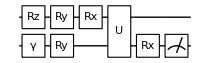

```mathematica
measxycirc=Flatten[{Subscript[measXY, 1][θ]}/. NVDevice[Aliases]]
DrawCircuit@%
```

```mathematica
ρ2=CreateDensityQureg[2];
```

```mathematica
(* test the circuit *)
Table[
parammeas=param;
(* set initial state as the perfect state and maximally mixed on electron *)
initρ=KroneckerProduct[xyDensityMatrix[param],{{0.5,0},{0,0.5}}];
Flatten@Table[
SetQuregMatrix[ρ2,initρ];
ApplyCircuit[ρ2,measxycirc/.θ->parammeas],
50],
{param, {0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4}}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## GRAPHIX noise extraction: measurement in XY basis on nuclear spin

### Noisy measurement

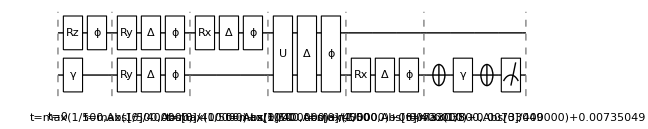

```mathematica
noisymeasurement=InsertCircuitNoise[{Subscript[measXY, 1][θ]},NVCenterDelft[FreqWeakZZ->False,StdPassiveNoise->False],ReplaceAliases->True];
DrawCircuit@%
```

```mathematica
NVNoise["durRead"]=Table[First@Last@noisymeasurement/.θ->j π/4,{j,0,7}]
```

{0.00935049,0.00935049,0.00935049,0.00935049,0.00935049,0.00935049,0.00935049,0.00935049}

```mathematica
(* test the circuit: FIDELITY of measurement is around 0.934, without decay and cross-talk :O  *)
(* set initial state as the perfect state and maximally mixed on electron *)
initρ=KroneckerProduct[xyDensityMatrix[π],{{0.5,0},{0,0.5}}];
circ=DeleteCases[ExtractCircuit[noisymeasurement/.θ->π],Subscript[M, _]];
SetQuregMatrix[ρ2,initρ];
ApplyCircuit[ρ2,circ];
ρ2mat=GetQuregState[ρ2];
Re[ρ2mat[[1,1]]+ρ2mat[[3,3]]]
```

0.934127

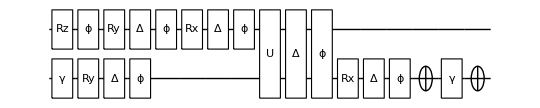

```mathematica
(* measinv o noisymeas = efffective noise on measurement*)
noisymeas=Join[DeleteCases[ExtractCircuit@noisymeasurement,Subscript[M, _]]];
DrawCircuit@%
```

```mathematica
(* Check performance of the noisy measurement  *)
ngRead=Table[
param={θ->j π/4};
circ=noisymeas/.param;
(* initialise to state +θ and measure *)
initρ=KroneckerProduct[xyDensityMatrix[θ/.param],{{0.5,0},{0,0.5}}];
SetQuregMatrix[ρ2,initρ];
ApplyCircuit[ρ2,circ];
ρ2mat=GetQuregState[ρ2];
Print@Re[ρ2mat[[1,1]]+ρ2mat[[3,3]]];
superopmeas=CalcCircuitMatrix[noisymeas/.param];
 krausmeas=Chop@ChoiToKraus@ColumnShuffle@superopmeas;
ToString[j]->{Re@krausmeas,Im@krausmeas}
,{j,0,7}];
```

0.934266

0.934231

0.934197

0.934162

0.934127

0.934093

0.934058

0.934024

```mathematica
NVNoise["ngRead"]=ngRead;
```

```mathematica
config=Association@Options@NVCenterDelft
```

<|QubitNum→4,T1→<|0→3600,1→60,2→60,3→60|>,T2→<|0→1.5,1→10,2→10,3→10|>,FreqWeakZZ→5,FreqSingleXY→<|0→15000000,1→500,2→500,3→500|>,FreqSingleZ→<|0→32000000,1→400000,2→400000,3→400000|>,FreqCRot→<|1→1500.,2→2800.,3→800.|>,FidCRot→<|1→0.98,2→0.98,3→0.98|>,FidSingleXY→<|0→0.9995,1→0.995,2→0.995,3→0.99|>,FidSingleZ→<|0→0.9999,1→0.9999,2→0.99999,3→0.9999|>,EFSingleXY→{0.75,0.25},EFCRot→{0.9,0.1},FidInit→0.999,DurInit→1/500,FidMeas→0.946,DurMeas→1/50000,StdPassiveNoise→True|>

```mathematica
NVNoise["T1"]=List@@config[T1];
NVNoise["T2"]=List@@config[T2];
NVNoise["crosstalk"]=config[FreqWeakZZ];
```

```mathematica
Keys@NVNoise
```

{description,ngPrep,durPrep,ngCZ,durCZ,durRead,ngRead,T1,T2,crosstalk}

```mathematica
Export["NVNoise.json",Normal@NVNoise]
```

NVNoise.json

```mathematica
(* double check *)
Table[
klist=ngRead[[j]][[2]];
kmap=klist[[1]]+ⅈ klist[[2]];
MatrixForm@Chop@Total[ConjugateTranspose[#].# &/@kmap]
,{j,8}]
```

{(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)}